# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}]
$Path=Join[$Path,FileNames[packageDirectory]];
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\1DPackage\*

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedNewMethod","ConstrainedCorrelation"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseAEREAL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Aereal",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
reduce=2;
path1=FileNameJoin[{baseAEREAL,"Aereal1.png"}];
path2=FileNameJoin[{baseAEREAL,"Aereal2.png"}];
pathResult=FileNameJoin[{baseAEREAL,"AerealResult.png"}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];

reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];

iaa=reduire[ColorConvert[clean@Import[path1],"GrayScale"],reduce];
ibb=reduire[ColorConvert[clean@Import[path2],"GrayScale"],reduce];
iccolor=reduire[clean@Import[pathResult],reduce];

Show[iaa]
```

-Graphics-

## Image sections

```mathematica
(*{1,44},{1,102} arbitrary size to make the method faster *)
listDims={{500,500}}
ims=Table[
nx=dims[[1]]/reduce;
ny=dims[[2]]/reduce;

tim=4;
{ia,ib,icolor}=ImageTake[#,{ny,ny+44*tim},{nx,nx+102*tim}]&/@{iaa,ibb,iccolor};

{ia,ib}
,{dims,listDims}]
```

{{500,500}}

{{-Graphics-,-Graphics-}}

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## Little functions

```mathematica
bigTest[steps_,dis_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[

depth=stereoDepth[n,u,listv0,condition,im[[1]],im[[2]],minmax[[2]],minmax,Range[1,1+102*tim,steps],Range[1,1+44*tim],e,"ConstrainedCorrelation"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,1+44*tim}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,1+44*tim}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,1+44*tim}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,1+44*tim}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,1+44*tim}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,1+44*tim}];

(* We create g0 *)
g0=Graphics[{PointSize[0.003],Table[affiche[#,1+44*tim-y]&/@realPVTable[[y]],{y,1,1+44*tim}]}];
g0=Rasterize[Show[im[[1]],g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## Big Tests

### Test Design

For a synthetical displacement of 0.1:
 
•	Initial values range: {{0,1},{-1,1},{-1,0},{-2,2}}
•	Selection criteria:
	•	We filter direction (positive solutions only)
	•	Range {0, 1} 
	•	No errors allowed
•	Magnitude threshold for gradient is e=0.0001

(* Criterias to select a solution *)

newValCon=Select[tableNewVals,(#[[3]]==”converged”&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValAny=Select[tableNewVals,((#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&&#[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValOk=Select[tableNewVals,((#[[3]]==”ok”||#[[3]]==”oksign”||#[[3]]==”okmag”)&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
noFakeConverge=Select[tableNewVals,(#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&,1];

### Test Run

```mathematica
(* Test values *)
testLevels={{1,1}};
dis=0.1;
e=0.0001;
n=0;
u=0;
steps=1;
```

```mathematica
(* Creating initial values *)
v0Range={0,1};
r=Random[];
listv0=Select[RandomReal[v0Range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[v0Range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
```

```mathematica
(* Creating condition *)
topbot={0,1};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Scaling results *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
```

```mathematica
levelTable=Table[


bigTest[steps,dis,n,u,listv0,condition,e,{levels},ims]

,{levels,testLevels}];
```

```mathematica
(*selectrion criteria, level, image, extra, kind of result, rows *)
Dimensions[levelTable]
```

{1,1,1,4}

```mathematica
levelTable[[1,1,1,3,All,All,2]];
```

### Images

```mathematica
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
imagesTable=Table[

images=ConformImages[Rasterize[Image[#],ImageResolution->500]&/@Flatten[{ims[[which,1;;2]],levelTable[[1,which,1,4]]}],{4000}]

,{which,Length[ims]}];

imFinal=Legended[Grid[imagesTable],legendBar]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
showMove[ims[[1,2]],ims[[1,1]],{0,1}]
```

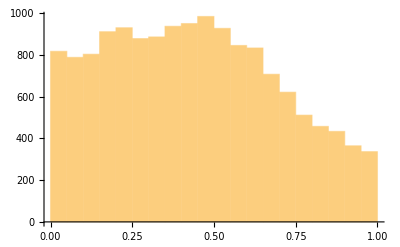

0.438093

0.259563

```mathematica
Histogram[Flatten[levelTable[[1,1,1,1,All,All,2]]]]
Mean[Flatten[levelTable[[1,1,1,1,All,All,2]]]]
StandardDeviation[Flatten[levelTable[[1,1,1,1,All,All,2]]]]
```

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],imFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\synaereal-im.pdf

### More in depth

```mathematica
lvl=5;
```

```mathematica
k=15;
{ka,kb}=ImageData[#][[k]]&/@ims[[1]];
pyra=pyrFuncGen[ka,lvl];
pyrb=pyrFuncGen[kb,lvl];
pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];
```

```mathematica
showMove[ims[[1,1]],ims[[1,2]],{-3,3}];
```

```mathematica
lineTest[n,u,listv0,condition,Range[1,ImageDimensions[ia][[1]]],pyrab[[1;;1]],e,"ConstrainedCorrelation"]
```

{{0.13095,0.125476,converged,1},{0.13185,0.139798,converged,2},{0.166793,0.184022,converged,3},{0.230822,0.237803,converged,4},{0.247774,0.181535,converged,5},{0.,0.,sign,6},{0.,0.,sign,7},{0.,0.,fakeconverged,8},{0.046902,0.0475396,converged,9},{0.,0.,fakeconverged,10},{0.00251398,0.00507123,converged,11},{0.0319055,0.0295205,converged,12},{0.,0.,sign,13},{0.171082,0.147162,converged,14},{0.106254,0.120191,converged,15},{0.,0.,sign,16},{0.0558303,0.0724328,converged,17},{0.0838383,0.0825799,converged,18},{0.,0.,corr,19},{0.193292,0.214837,converged,20},{0.178532,0.187299,converged,21},{0.216087,0.214576,converged,22},{0.292327,0.26325,converged,23},{0.470456,0.485142,converged,24},{0.,0.,sign,25},{0.0390966,0.0825455,converged,26},{0.13855,0.182093,converged,27},{0.20782,0.211012,converged,28},{0.237371,0.190786,converged,29},{0.280798,0.66809,converged,30},{0.,0.,corr,31},{0.,0.,sign,32},{0.,0.,sign,33},{0.33771,0.386014,converged,34},{0.308776,0.31107,converged,35},{0.343709,0.34886,converged,36},{0.,0.,sign,37},{0.,0.,corr,38},{0.,0.,sign,39},{0.,0.,sign,40},{0.038918,0.079416,converged,41},{0.187143,0.238264,converged,42},{0.362844,0.380403,converged,43},{0.189891,0.538769,converged,44},{0.,0.,sign,45},{0.,0.,corr,46},{0.,0.,sign,47},{0.113339,0.2746,converged,48},{0.321871,0.449483,converged,49},{0.419669,0.518332,converged,50},{0.459979,0.425623,converged,51},{0.42843,0.371495,converged,52},{0.460515,0.400664,converged,53},{0.556,0.417336,converged,54},{0.,0.,sign,55},{0.,0.,corr,56},{0.,0.,mag,57},{0.,0.,corr,58},{0.,0.,sign,59},{0.,0.,mag,60},{0.,0.,mag,61},{0.0738074,0.0955283,converged,62},{0.0521109,0.0631535,converged,63},{0.044894,0.0380552,converged,64},{0.,0.,sign,65},{0.,0.,corr,66},{0.,0.,fakeconverged,67},{0.,0.,sign,68},{0.,0.,sign,69},{0.100312,0.162132,converged,70},{0.232942,0.286395,converged,71},{0.346427,0.341769,converged,72},{0.,0.,sign,73},{0.,0.,sign,74},{0.,0.,corr,75},{0.,0.,sign,76},{0.428829,0.101075,ok,77},{0.0564063,0.0801272,converged,78},{0.185568,0.271005,converged,79},{0.,0.,sign,80},{0.050627,0.101254,converged,81},{0.136166,0.150989,converged,82},{0.182461,0.204929,converged,83},{0.222231,0.149652,converged,84},{0.,0.,mag,85},{0.432816,0.282603,converged,86},{0.152429,0.442349,converged,87},{0.291997,0.314125,converged,88},{0.257503,0.219546,converged,89},{0.292165,0.364317,converged,90},{0.0319893,0.0609197,converged,91},{0.0944832,0.339323,converged,92},{0.,0.,sign,93},{0.,0.,sign,94},{0.142056,0.243252,converged,95},{0.292138,0.34265,converged,96},{0.371649,0.313038,converged,97},{0.,0.,corr,98},{0.,0.,corr,99},{0.0844839,0.186292,converged,100},{0.263102,0.268266,converged,101},{0.23851,0.239608,converged,102},{0.260036,0.257931,converged,103},{0.,0.,sign,104},{0.,0.,fakeconverged,105},{0.,0.,fakeconverged,106},{0.546012,0.425409,converged,107},{0.313709,0.347614,converged,108},{0.234043,0.171602,converged,109},{0.,0.,sign,110},{0.,0.,sign,111},{0.34009,0.272699,converged,112},{0.0812247,0.169031,converged,113},{0.226458,0.306734,converged,114},{0.0583212,0.139628,converged,115},{0.2079,0.250528,converged,116},{0.273103,0.244376,converged,117},{0.249305,0.221501,converged,118},{0.302725,0.353513,converged,119},{0.416244,0.407067,converged,120},{0.476668,0.418511,converged,121},{0.612567,0.377251,converged,122},{0.214817,0.549929,converged,123},{0.,0.,sign,124},{0.0764467,0.141034,converged,125},{0.142601,0.208455,converged,126},{0.248134,0.279462,converged,127},{0.410315,0.343944,converged,128},{0.144589,0.233477,converged,129},{0.197958,0.201457,converged,130},{0.246846,0.30126,converged,131},{0.,0.,sign,132},{0.,0.,sign,133},{0.0573482,0.14832,converged,134},{0.152325,0.0497379,converged,135},{0.,0.,mag,136},{0.,0.,fakeconverged,137},{0.,0.,mag,138},{0.,0.,mag,139},{0.,0.,sign,140},{0.,0.,sign,141},{0.,0.,fakeconverged,142},{0.,0.,fakeconverged,143},{0.,0.,fakeconverged,144},{0.,0.,fakeconverged,145},{0.,0.,fakeconverged,146},{0.,0.,fakeconverged,147},{0.,0.,fakeconverged,148},{0.,0.,fakeconverged,149},{0.,0.,sign,150},{0.,0.,sign,151},{0.,0.,sign,152},{0.,0.,sign,153},{0.,0.,fakeconverged,154},{0.,0.,fakeconverged,155},{0.,0.,fakeconverged,156},{0.,0.,fakeconverged,157},{0.,0.,fakeconverged,158},{0.,0.,sign,159},{0.,0.,sign,160},{0.,0.,sign,161},{0.,0.,sign,162},{0.,0.,fakeconverged,163},{0.43722,0.163153,converged,164},{0.158642,0.238989,converged,165},{0.,0.,fakeconverged,166},{0.,0.,fakeconverged,167},{0.,0.,fakeconverged,168},{0.,0.,fakeconverged,169},{0.,0.,sign,170},{0.,0.,corr,171},{0.349832,0.548632,converged,172},{0.,0.,sign,173},{0.,0.,fakeconverged,174},{0.493086,0.254897,converged,175},{0.,0.,fakeconverged,176},{0.,0.,fakeconverged,177},{0.,0.,fakeconverged,178},{0.,0.,fakeconverged,179},{0.0289248,0.0449667,converged,180},{0.135312,0.133294,converged,181},{0.0517,0.0441371,converged,182},{0.,0.,fakeconverged,183},{0.,0.,fakeconverged,184},{0.141186,0.245709,converged,185},{0.,0.,sign,186},{0.,0.,sign,187},{0.,0.,sign,188},{0.,0.,mag,189},{0.,0.,sign,190},{0.,0.,sign,191},{0.,0.,corr,192},{0.,0.,sign,193},{0.,0.,sign,194},{0.,0.,sign,195},{0.,0.,corr,196},{0.,0.,sign,197},{0.,0.,sign,198},{0.0939593,0.313734,converged,199},{0.,0.,mag,200},{0.,0.,corr,201},{0.,0.,sign,202},{0.,0.,fakeconverged,203},{0.,0.,sign,204},{0.,0.,mag,205},{0.,0.,corr,206},{0.,0.,sign,207},{0.,0.,sign,208},{0.,0.,mag,209},{0.,0.,sign,210},{0.,0.,sign,211},{0.,0.,sign,212},{0.,0.,corr,213},{0.,0.,sign,214},{0.,0.,sign,215},{0.,0.,corr,216},{0.,0.,mag,217},{0.,0.,sign,218},{0.,0.,fakeconverged,219},{0.748748,0.0890975,converged,220},{0.,0.,sign,221},{0.,0.,mag,222},{0.,0.,sign,223},{0.,0.,corr,224},{0.230294,0.233114,converged,225},{0.,0.,sign,226},{0.,0.,sign,227},{0.,0.,sign,228},{0.,0.,mag,229},{0.,0.,sign,230},{0.,0.,mag,231},{0.438255,0.345366,converged,232},{0.,0.,sign,233},{0.,0.,corr,234},{0.,0.,sign,235},{0.,0.,sign,236},{0.,0.,sign,237},{0.,0.,sign,238},{0.,0.,fakeconverged,239},{0.197466,0.468301,converged,240},{0.,0.,sign,241},{0.,0.,sign,242},{0.,0.,fakeconverged,243},{0.,0.,mag,244},{0.,0.,sign,245},{0.,0.,fakeconverged,246},{0.,0.,fakeconverged,247},{0.,0.,sign,248},{0.,0.,sign,249},{0.,0.,sign,250},{0.,0.,sign,251},{0.,0.,sign,252},{0.,0.,sign,253},{0.171431,0.571799,converged,254},{0.492309,0.230062,converged,255},{0.,0.,mag,256},{0.,0.,sign,257},{0.,0.,fakeconverged,258},{0.,0.,fakeconverged,259},{0.383213,0.341519,converged,260},{0.40155,0.44714,converged,261},{0.,0.,fakeconverged,262},{0.,0.,sign,263},{0.,0.,mag,264},{0.,0.,mag,265},{0.,0.,sign,266},{0.,0.,fakeconverged,267},{0.,0.,fakeconverged,268},{0.,0.,fakeconverged,269},{0.,0.,fakeconverged,270},{0.,0.,corr,271},{0.,0.,sign,272},{0.,0.,sign,273},{0.0196183,0.0256841,converged,274},{0.0854339,0.103681,converged,275},{0.,0.,mag,276},{0.,0.,fakeconverged,277},{0.,0.,fakeconverged,278},{0.0154546,0.0160089,converged,279},{0.,0.,fakeconverged,280},{0.,0.,fakeconverged,281},{0.0317174,0.0374718,converged,282},{0.,0.,fakeconverged,283},{0.,0.,fakeconverged,284},{0.0705618,0.106567,converged,285},{0.241569,0.253657,converged,286},{0.153397,0.0888446,converged,287},{0.,0.,fakeconverged,288},{0.0896554,0.142408,converged,289},{0.142183,0.107744,converged,290},{0.,0.,fakeconverged,291},{0.,0.,sign,292},{0.,0.,corr,293},{0.320199,0.257262,converged,294},{0.0259851,0.0300978,converged,295},{0.0110428,0.0164731,converged,296},{0.0571428,0.0622332,converged,297},{0.00348632,0.00531574,converged,298},{0.0800835,0.084926,converged,299},{0.,0.,sign,300},{0.,0.,sign,301},{0.,0.,sign,302},{0.0868187,0.11465,converged,303},{0.,0.,sign,304},{0.,0.,corr,305},{0.,0.,fakeconverged,306},{0.,0.,fakeconverged,307}}

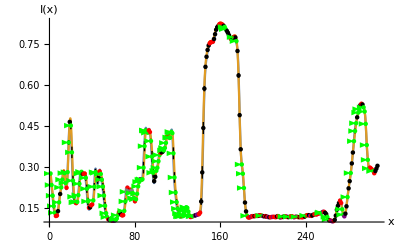

```mathematica
seeAllLine[n,u,listv0,condition,Range[1,1+102*tim],pyrab[[1;;1]],e,"ConstrainedCorrelation"]
```

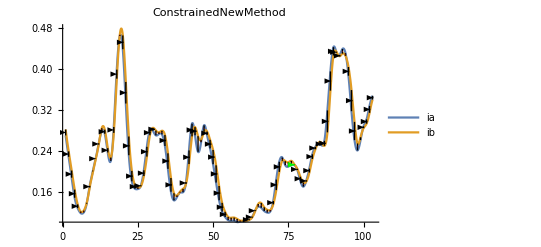

```mathematica
seeAllLine[n,u,listv0,condition,Range[1,103],pyrab[[1;;1]],e,"ConstrainedNewMethod"]
```